# Patterns in N-Body Simulations: Statistical Analysis of the Three Body Problem

## Dissecting NBodySimulations outputs, statistically inspecting, and classifying them.

Pedro Gomes Cabral, Katja Della Libera.

ABSTRACT: In this project, I analyze n-body simulations outputs and their patterns by utilizing different statistical methods, visualization algorithms, and feature extraction techniques. Using an n-body simulation random generation technique, a sample of 5000 different outputs could be generated. By performing feature extraction processes, some interesting visualizations about the different outcomes from the simulations were plotted on a two-dimensional feature space plot. Additional conclusions were made using the distribution of the center-of-mass, and a two-body mass visualization.

## Introduction

In physics and astronomy, an N-body simulation is a simulation of a dynamical system of particles, usually under the influence of physical forces, such as gravity. Currently, computing power is sufficient for processing some classes of N-Body simulations, with a small number of bodies, and with a short lapse time. For cases of realistic units such as astronomical units and gigayears, computers can’t handle their complexity. A way to prevent this computational complexity difficulty, systems such as “InverseSquare” relativistically treat metric units and unitless quantities mathematically equivalent.

Here are some cases of random n-body simulations, they have an extraordinarily chaotic behavior, and are vulnerable to having their outputs changed with just a few tweaks on their initial states.

NBodyPlot — Creates a function for easily visualizing an n-body simulation using parametric plotting.

```mathematica
NBodyPlot[data_] := ParametricPlot[Evaluate[data[All, "Position", t]],{t, 0, data["SimulationTime"]}, AspectRatio -> Automatic, Axes -> False, PlotStyle -> {Thickness[0.025], Thickness[0.025], Thickness[0.025]}]
```

CreateRandomPivot — Creates a function for generating a random unitless heavy object.

```mathematica
CreateRandomPivot[] := Block[{},
	<|"Mass" -> 1, "Position" -> {0, 0}, "Velocity" -> RandomReal[{-0.25, 0.25}, 2]|>
]
```

CreateRandomBody — Creates a function for generating a random unitless light object.

```mathematica
CreateRandomBody[] := Block[{},
	<|"Mass" -> RandomReal[{0.01, 0.99}], "Position" -> RandomReal[{-1, 1}, 2], "Velocity" -> RandomReal[{-1, 1}, 2]|>
]
```

Creates a table of visualizations for random n-body simulations.

```mathematica
Table[Rasterize[NBodyPlot[NBodySimulation["InverseSquare",{CreateRandomPivot[],CreateRandomBody[],CreateRandomBody[]},10]],ImageSize->Small],8]//Quiet
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

A really interesting way to visualize those orbits is to perform a ListAnimate in a sequence of images.

```mathematica
NBodySimulationVisualize[data_: Nothing, steps_: 1] := Block[{
	stepRange = Range[0.01, data["SimulationTime"], steps],
	nBodies = Length[data[All]]
	},
	PrintTemporary[Style["⇒", 15, Orange], " ",
		"Computing graphics for ",
		Style[ToString[nBodies] <> " bodies", Orange], " ",
		ProgressIndicator[Appearance -> "Percolate", ImageSize -> {60, 20}]
	];
	ListAnimate[
		ParametricPlot[Evaluate[data[All, "Position", t]], {t, 0, #}, AspectRatio -> Automatic,
			Axes -> False, PlotStyle -> {Thickness[0.025], Thickness[0.025], Thickness[0.025]}] & /@stepRange,
		Deployed -> True, Alignment -> Center, AnimationRunning -> False, SaveDefinitions -> True
	]
]
```

Creates an animated ParametricPlot visualization for a random three body simulation.

```mathematica
NBodySimulationVisualize[NBodySimulation["InverseSquare",{CreateRandomPivot[],CreateRandomBody[],CreateRandomBody[]},10],0.1] //Quiet
```

## Data Visualization

Using the methods on the “Data Generation Procedure” section, the following datasets can be generated. In this notebook, 5000 random samples are included.

Import “HeuristicData”, “NBParameters”, and “NBDPaths” from the notebook.

```mathematica
HeuristicData = ;
NBParameters = ;
NBDPaths = ;
```

Transform the “NBParameters” list into a dataset, and define as NBParametersDataset.

```mathematica
NBParametersDataset = Dataset@NBParameters;
```

The “HeuristicData” list contains lists of the heuristic results generated by the “NBodyHeuristics” function (see “Data Generation Procedure”), the “NBParameters” list contains lists of initial parameters, and the “NBDPaths” list contains lists of the final paths of the bodies. Every list is uniform and contains 5000 elements each.

Get the lenght of the three lists.

```mathematica
{Length@HeuristicData, Length@NBParameters, Length@NBDPaths}
```

{5000,5000,5000}

Split the three datasets as three different datasets for each body.

```mathematica
{NBPBodyA, NBPBodyB, NBPBodyC} = Table[NBParametersDataset⟦All, t⟧, {t, 1, 3}];
```

Position search every element on “HeuristicData” for all the possible combinations.

```mathematica
{allDoubleFalse, allSingleFalse, pivotDiverged, allContained, allDivergent} =
	Table[Join@@Position[HeuristicData, t], {t, {
		{False, True, False} | {False, False, True} | {True, False, False}, {False, True, True} | {True, False, True} | {True, True, False}, {False, True, True}, {True, True, True}, {False, False, False}
		}}];
```

With all the positions, get all the masses from the bodies B and C, then thread them.

```mathematica
{allDoubleFalsePoints, allSingleFalsePoints, allContainedPoints, allDivergentPoints, pivotDivergedPoints} = 
	Table[Thread[{Normal[NBPBodyB[x, "Mass"]], Normal[NBPBodyC[x, "Mass"]]}], {x, {allDoubleFalse, allSingleFalse, allContained, allDivergent, pivotDiverged}}];
```

List plot all the points that are contained (the simulations that orbit), all the points that diverge, all the pivots that diverge, and all diverging possibilities.

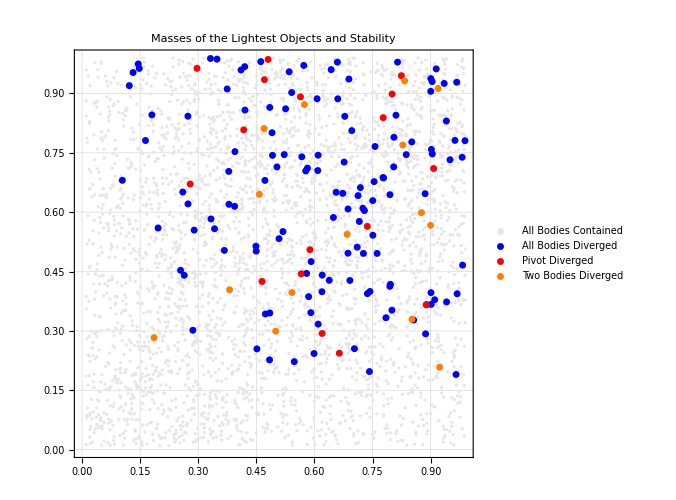

```mathematica
ListPlot[{allContainedPoints, allDivergentPoints, pivotDivergedPoints, allDoubleFalsePoints},PlotStyle -> {RGBColor[0.9, 0.9, 0.9], {PointSize[0.01], Blue}, {PointSize[0.01], Red}, {PointSize[0.01], Orange}}, AspectRatio -> Automatic, PlotTheme -> "Detailed", PlotLegends -> {"All Bodies Contained", "All Bodies Diverged", "Pivot Diverged", "Two Bodies Diverged"}, PlotLabel -> "Masses of the Lightest Objects and Stability", LabelStyle -> {16, GrayLevel[0]}, ImageSize -> {500, 500}]
```

With this plot, we can visualize that there’s is a correlation between the lighter bodies masses and the stability of the systems. The lightest bodies have the most stability in their simulations, which means that they are not “catapulted” from the system.

Now, let’s calculate the distances between the center of masses using C_m=(∑m_i*x_i)/(∑m_i) with m_i as the mass of the individual bodies and x_i as the positions in space.

Thread every single body mass with  their final positions.

```mathematica
centerOfMass=Thread[{Normal@NBParametersDataset⟦All,All,"Mass"⟧,NBDPaths}];
```

Create a Table the center of masses, using C_m=(∑m_i*x_i)/(∑m_i) for every single body.

```mathematica
centerOfMasses=Table[(centerOfMass⟦n⟧⟦1⟧*centerOfMass⟦n⟧⟦2⟧//Total)/Total[centerOfMass⟦n,1⟧],{n,1,Length[NBParametersDataset]}];
```

Get the EuclideanDistance of all center of masses and the final positions of the bodies.

```mathematica
distancesCOM=MapThread[Table[EuclideanDistance[#1,#2⟦n⟧],{n,1,3}]&,{centerOfMasses,NBDPaths}];
```

Plot a Histogram of all the distances between the center of mass and the bodies.

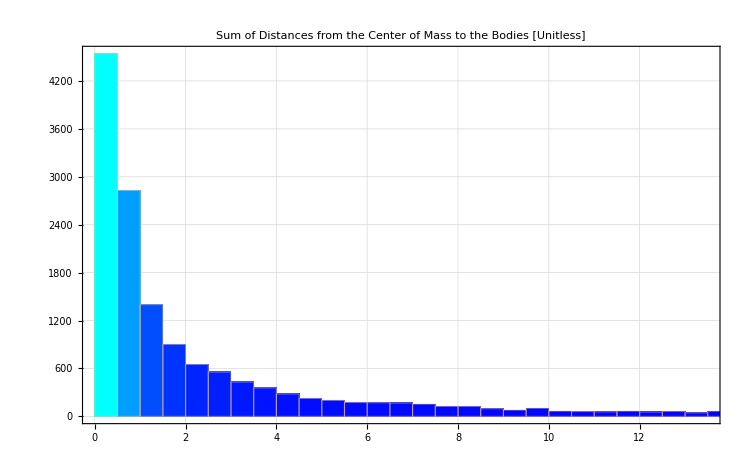

```mathematica
Histogram[Flatten@distancesCOM, PlotLabel -> "Sum of Distances from the Center of Mass to the Bodies [Unitless]", LabelStyle -> {16, GrayLevel[0]},
PlotTheme -> "Detailed", ColorFunction -> Function[{height}, RGBColor[0, 1 * height, 1]], ImageSize -> {750, 500}]
```

This histogram clearly shows that there’s a logarithmic curve of the distances from the center of mass and the objects, in fact, a distribution can be matched using FindDistribution[].

Find the distribution for the data contained in “distancesCOM”

```mathematica
FindDistribution[Flatten@distancesCOM]
```

LogNormalDistribution[0.102305,1.66635]

And, by plotting the histogram with a logarithmic scale, we obtain a normal distribution.

Plot a Histogram of all the distances between the center of mass and the bodies, logarithmically scaled.

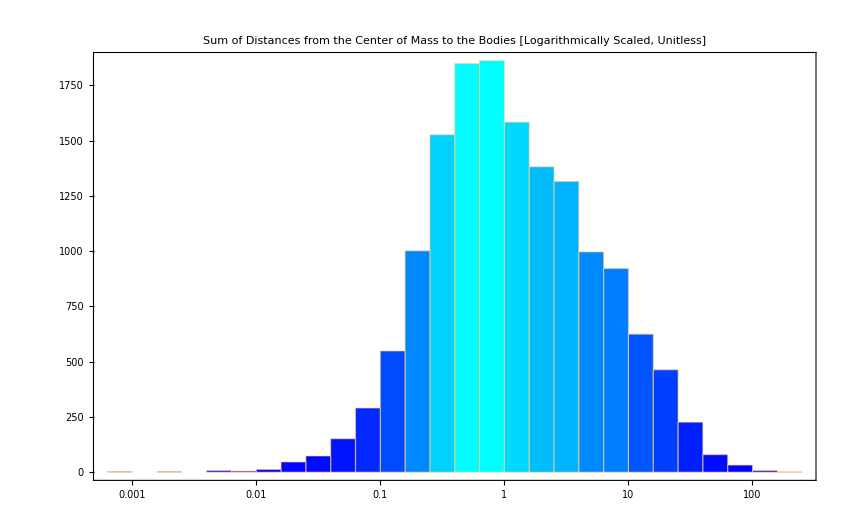

```mathematica
Histogram[Flatten@distancesCOM,{"Log",20},PlotLabel->"Sum of Distances from the Center of Mass to the Bodies [Logarithmically Scaled, Unitless]",LabelStyle->{16,GrayLevel[0]},PlotTheme->"Detailed",ColorFunction->Function[{height},RGBColor[0,1*height,1]],ImageSize -> {850, 500}]
```

One fascinating visualization is to FeatureSpacePlot all the rasterizations of the simulations. This should give us an interesting view of the bigger picture of the simulations.

Rasterize 250 random three body simulations from the “NBParametersDataset” dataset.

```mathematica
rasterizeList = Rasterize[NBodyPlot[NBodySimulation["InverseSquare", #, 10]]] &/@ Normal[RandomSample[NBParametersDataset, 250]] // Quiet;
```

Perform a two-dimensional feature extraction and plot all of the rasterizations based on their features.

```mathematica
FeatureSpacePlot[rasterizeList⟦1;;200⟧, LabelingSize -> 30, ImageSize -> {800, 800}, PlotLabel -> "Feature Space of 250 Three Body Simulations", LabelStyle -> {16, GrayLevel[0]}]
```

-Graphics-

Based on this FeatureSpacePlot[], we can infer that the most caotic simulations are located in the borders, and the divergent simulations are always on the side of where is the body diverging.

## Conclusion

In this project, I conclude that the applicability of algorithms such as neural networks and clustering classification is hard due to the chaotic nature of the n-body simulations, the volatility of such systems do not allow such thing as classification. Some inference could be achieved in the graphics and distributions, such as stability in lower masses, and the close center of mass from the systems.

## [Optional] Data Generation Procedure

For generating all the data used in this project, these cells can be executed, note that this section is an appendix, and not necessary since 5000 sample data are already included in this notebook.

### Generating Data Batches

Defines a “BatchPath” that will be used for the entirety of the project.

```mathematica
batchPath = NotebookDirectory[]
```

/home/jenkins/Documents/Projects/WolframSC2K19/Project/NBodyNN/Development/

Defines all the lists that will be used for the storing the generated data.

```mathematica
{generatedData, heuristicData, nbdpathsData, bodyData, bodiesData} = Table[{}, {5}];
```

Defines a “BatchCounter” that will be used for the counting and managing the batches.

```mathematica
batchCounter = 1;
```

Creates a function for heuristically determine if a body has diverged or not.

```mathematica
NBodyHeuristics[positionsList_,maxSpace_:8] := Block[{
  emptyList = {},
  bodyA = positionsList⟦1⟧,
  bodyB = positionsList⟦2⟧,
  bodyC = positionsList⟦3⟧
},
  If[maxSpace ≥ bodyA⟦1⟧ ≥ -maxSpace ∧ maxSpace ≥ bodyA⟦2⟧ ≥ -maxSpace,
    emptyList = Join[emptyList, {True}],
    emptyList = Join[emptyList, {False}]
  ];
  If[maxSpace ≥ bodyB⟦1⟧ ≥ -maxSpace ∧ maxSpace ≥ bodyB⟦2⟧ ≥ -maxSpace,
    emptyList = Join[emptyList, {True}],
    emptyList = Join[emptyList, {False}]
  ];
  If[maxSpace ≥ bodyC⟦1⟧ ≥ -maxSpace ∧ maxSpace ≥ bodyC⟦2⟧ ≥ -maxSpace,
    emptyList = Join[emptyList, {True}],
    emptyList = Join[emptyList, {False}]
  ];
  Return[emptyList];
]
```

Creates a function for generating all the batches.

```mathematica
GenerateNBodySimulations[nsimulations_,time_] := Do[AbortProtect[
	PrintTemporary[Style["⇒", 15, Orange], " ",
		"Generated ", Dynamic[Length[heuristicData]], " ", Style["NBodySimulations", Orange], " ",
		ProgressIndicator[Appearance -> "Percolate", ImageSize -> {60, 20}]
	];
	bodyData = {CreateRandomPivot[], CreateRandomBody[], CreateRandomBody[]};
	generatedData = NBodySimulation["InverseSquare", bodyData, time] // Quiet;
	heuristicData = Append[heuristicData, NBodyHeuristics[generatedData[All, "Position", generatedData["SimulationTime"]]]];nbdpathsData = Append[nbdpathsData, generatedData[All, "Position", generatedData["SimulationTime"]]]];bodiesData = Append[bodiesData, bodyData];
	ClearAll[generatedData, bodyData],
	nsimulations
];
```

Generates one batch of 100 simulations, of 10 seconds each.

```mathematica
GenerateNBodySimulations[100, 10];
```

Exports the results, and resets the variables for the next batch.

```mathematica
Export[batchPath <> "HeuristicData_" <> ToString[batchCounter] <> ".mx", heuristicData];
Export[batchPath <> "NBDPaths_" <> ToString[batchCounter] <> ".mx", nbdpathsData];
Export[batchPath <> "NBParameters_" <> ToString[batchCounter] <> ".mx", bodiesData];
{generatedData,heuristicData,nbdpathsData,bodyData,bodiesData}=Table[{},{5}];
batchCounter++;
```

### Assembling the Data Batches

```mathematica
JoinListFiles[fileName_,numberRange_] := Join@@Table[Import[batchPath <> fileName <> "_" <> ToString[n] <> ".mx"], {n, 1, numberRange}]
```

```mathematica
NBParameters = JoinListFiles["NBParameters", 50];
HeuristicData = JoinListFiles["HeuristicData", 50];
NBDPaths = JoinListFiles["NBDPaths", 50];
```

#### [Optional] Saving the Assembled Data Batches

For future usage, an optional procedure to perform is to save the assembled files into a single file, but this step is arbitrary to the whole process.

```mathematica
Export[batchPath <> "HeuristicData.mx", HeuristicData];
Export[batchPath <> "NBDPaths.mx", NBDPaths];
Export[batchPath <> "NBParameters.mx", NBParameters];
```

And eventualy, the files can be read by importing them.

```mathematica
HeuristicData = Import[batchPath <> "HeuristicData.mx"];
NBParameters = Import[batchPath <> "NBParameters.mx"];
NBDPaths = Import[batchPath <> "NBDPaths.mx"];
```